```mathematica
Clear[young,nu]
From3DToVoigt[tensor_]:={tensor[[1,1]],tensor[[2,2]],tensor[[1,2]],tensor[[3,3]]};
FromVoigtTo3D[vec_]:={{vec[[1]],vec[[3]],0},{vec[[3]],vec[[2]],0},{0,0,vec[[4]]}};
(*FromVoigtTo3DPlaneStrainStress[vec_]:={{vec[[1]],vec[[3]],0},{vec[[3]],vec[[2]],0},{0,0,nu (vec[[2]]+vec[[1]])}};
FromVoigtTo3DPlaneStrainStrain[vec_]:={{vec[[1]],vec[[3]],0},{vec[[3]],vec[[2]],0},{0,0,0}};*)

(*epsp={{0.000040550224568711,0.,0.},{0.,-0.0000202751,0.},{0.,0.,-0.000020275112}};
epst={{0.0011319839999999,0,0},{0,0,0},{0,0,0}};
epss=epst-epsp;
young=210000;
sigy=210;
nu=0.;
*)
lambda=young nu/((1+nu)(1-2nu));
mu=young/(2(1+nu));
K=(young)/(3*(1-2nu));
G=young/(2(1+nu));
epss={{epsxx,epsxy,0},{epsxy,epsyy,0},{0,0,0}};
sigma=lambda Tr[epss]IdentityMatrix[3]+ 2 mu epss;
From3DToVoigt[sigma];
P=K Tr[epss];
S=sigma-1/3 Tr[sigma]IdentityMatrix[3];
Simplify[sigma-(P IdentityMatrix[3]+ S)]
Simplify[epss-(1/(2G) S + 1/3 Tr[epss]IdentityMatrix[3])]

p1=young/((1+nu)(1-2nu));
De=p1({{1-nu, nu, 0, nu}, {nu, 1-nu, 0, nu}, {0, 0, (1-2nu), 0}, {nu, nu, 0, 1-nu}});
sol1=De.{epsxx,epsyy,epsxy,0};
Simplify[From3DToVoigt[sigma]-sol1]
Simplify[sigma-FromVoigtTo3D[sol1]]


p1=young/((1+nu)(1-2nu));
De2=p1({{1-nu, nu, nu, 0}, {nu, 1-nu, nu, 0}, {nu, nu, 1-nu, 0}, {0, 0, 0, (1-2nu)}});
sol2=De2.{epsxx,epsyy,0,epsxy};
Simplify[From3DToVoigt[sigma]-{sol2[[1]],sol2[[2]],sol2[[4]],sol2[[3]]}]
Simplify[sigma-FromVoigtTo3D[{sol2[[1]],sol2[[2]],sol2[[4]],sol2[[3]]}]]

J2=1/2 Tr[S.S];
q=Sqrt[3J2]//Simplify;
From3DToVoigt[sigma]//Simplify;
s=From3DToVoigt[S]//Simplify;
Simplify[q-(Sqrt[3/2(S[[1,1]]^2 +S[[2,2]]^2 +2S[[2,1]]^2 + S[[3,3]]^2)])]
Simplify[q-(Sqrt[3/2(s[[1]]^2 +s[[2]]^2 +2s[[3]]^2 + s[[4]]^2)])]
Ndir=s/Sqrt[s.s]//Simplify;
```

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

{0,0,0,0}

{{0,0,0},{0,0,0},{0,0,0}}

{0,0,0,0}

{{0,0,0},{0,0,0},{0,0,0}}

0

0

```mathematica
sigma
```

```mathematica
epss={{epsxx,epsxy,0},{epsxy,epsyy,0},{0,0,0}};
sigma=lambda Tr[epss]IdentityMatrix[3]+ 2 mu epss;
sigma//Simplify
```

{{((epsxx (-1+nu)-epsyy nu) young)/(-1+nu+2 nu^2),(epsxy young)/(1+nu),0},{(epsxy young)/(1+nu),((epsyy (-1+nu)-epsxx nu) young)/(-1+nu+2 nu^2),0},{0,0,-((epsxx+epsyy) nu young)/(-1+nu+2 nu^2)}}

```mathematica
Clear[young,nu]
From3DToVoigtPS[tensor_]:={tensor[[1,1]],tensor[[2,2]],tensor[[1,2]]};
FromVoigtTo3DPS[vec_]:={{vec[[1]],vec[[3]],0},{vec[[3]],vec[[2]],0},{0,0,0}};
(*FromVoigtTo3DPlaneStrainStress[vec_]:={{vec[[1]],vec[[3]],0},{vec[[3]],vec[[2]],0},{0,0,nu (vec[[2]]+vec[[1]])}};
FromVoigtTo3DPlaneStrainStrain[vec_]:={{vec[[1]],vec[[3]],0},{vec[[3]],vec[[2]],0},{0,0,0}};*)

(*epsp={{0.000040550224568711,0.,0.},{0.,-0.0000202751,0.},{0.,0.,-0.000020275112}};
epst={{0.0011319839999999,0,0},{0,0,0},{0,0,0}};
epss=epst-epsp;
young=210000;
sigy=210;
nu=0.;
*)
lambda=young nu/((1+nu)(1-2nu));
mu=young/(2(1+nu));
K=(young)/(3*(1-2nu));
G=young/(2(1+nu));
epss={{epsxx,epsxy,0},{epsxy,epsyy,0},{0,0,-nu/(1-nu) (epsxx+epsyy)}};
sigma=(lambda Tr[epss]IdentityMatrix[3]+ 2 mu epss);

From3DToVoigt[sigma];
P=K Tr[epss];
S=sigma-1/3 Tr[sigma]IdentityMatrix[3];

epss2=(S/(2G) + P/(3K) IdentityMatrix[3]);

Simplify[sigma-(P IdentityMatrix[3]+ S)]
Simplify[epss-(1/(2G) S + 1/3 Tr[epss]IdentityMatrix[3])]

De=({{young/(1-nu^2), (nu young)/(1-nu^2), 0}, {(nu young)/(1-nu^2), young/(1-nu^2), 0}, {0, 0, young/(1+ nu)}});
sol1=De.{epsxx,epsyy,1/2epsxy};
Simplify[From3DToVoigtPS[(sigma)]-sol1]
Simplify[sigma-FromVoigtTo3DPS[sol1]]
```

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

{0,0,(epsxy young)/(2+2 nu)}

{{0,(epsxy young)/(2+2 nu),0},{(epsxy young)/(2+2 nu),0,0},{0,0,0}}

```mathematica
sol1//Simplify
```

{-((epsxx+epsyy nu) young)/(-1+nu^2),-((epsyy+epsxx nu) young)/(-1+nu^2),(2 epsxy young)/(1+nu)}

```mathematica
sigma//Simplify
From3DToVoigtPS[sigma]//Simplify
```

{{-((epsxx+epsyy nu) young)/(-1+nu^2),(epsxy young)/(1+nu),0},{(epsxy young)/(1+nu),-((epsyy+epsxx nu) young)/(-1+nu^2),0},{0,0,0}}

{-((epsxx+epsyy nu) young)/(-1+nu^2),-((epsyy+epsxx nu) young)/(-1+nu^2),(epsxy young)/(1+nu)}

```mathematica
P//Simplify
```

-((epsxx+epsyy) young)/(3 (-1+nu))

```mathematica
S//Simplify
```

{{((epsyy+epsxx (-2+nu)-2 epsyy nu) young)/(3 (-1+nu^2)),(epsxy young)/(1+nu),0},{(epsxy young)/(1+nu),((epsxx+epsyy (-2+nu)-2 epsxx nu) young)/(3 (-1+nu^2)),0},{0,0,((epsxx+epsyy) young)/(3 (-1+nu))}}

```mathematica
From3DToVoigtPS[S]//Simplify
```

{((epsyy+epsxx (-2+nu)-2 epsyy nu) young)/(3 (-1+nu^2)),((epsxx+epsyy (-2+nu)-2 epsxx nu) young)/(3 (-1+nu^2)),(epsxy young)/(1+nu)}

```mathematica
q//Simplify
```

√(((epsxx^2+3 epsxy^2-epsxx epsyy+epsyy^2) young^2)/(1+nu)^2)

```mathematica
ApplyStrainComputeStressPlaneStress[epst_,epsp_,young_,nu_,epbarn_]:=Block[{d,resnor,counter,ddgamma,epbar,sigy,q,H=0,G,K,trialstrain,updatedstrain,trialstress,S,P,j2,phi,gamma,updatedstress,hardeningvariable,Dep,qtr,Str,trSS,tol,sigxx,sigyy,sigxy,Nvec,epsxx,epsyy,epsxy,sigzz,lambda,mu},

Sigma[eps_]:=lambda Tr[eps]IdentityMatrix[3]+2 mu eps;
G=(young)/(2*(1+nu));
K=(young)/(3*(1-2nu));
lambda=young nu/((1+nu)(1-2nu));
mu=young/(2(1+nu));

trialstrain=(epst-epsp);

{epsxx,epsyy,epsxy}=From3DToVoigtPS[trialstrain];

trialstress={{-((epsxx+epsyy nu) young)/(-1+nu^2),(epsxy young)/(1+nu),0},{(epsxy young)/(1+nu),-((epsyy+epsxx nu) young)/(-1+nu^2),0},{0,0,0}};

hardeningvariable=epbarn;

P=1/3 Tr[trialstress];
S=sigma-1/3 Tr[sigma]IdentityMatrix[3];
J2=1/2 Tr[S.S];
q=Sqrt[3 J2];

Nvec=S/Norm[S];
{sigy,H}= PLFUN[epbarn,data];
phi=q-sigy;
gamma=0;
If[phi≥ 0,
counter=1;
epbar=epbarn;
(*Print[" epbar  = ",epbar];*)
resnor=1;
tol=10^-5;
While[resnor≥ tol && counter<30,
{sigy,H}=PLFUN[epbar,data];
(*{sigy,H}={210,0};*)
d=-3 G-H;
ddgamma=-phi/d;
gamma=gamma-(phi/d);
epbar=epbar+ddgamma;
phi=q-3 gamma G - sigy;
resnor=Abs[phi/sigy];
counter++;

];
Mult=(1-((gamma 3 G )/q));
(*Print["milt = ",Mult];*)
S=Mult S;
updatedstrain=(1/(2G) S+ 1/3 Tr[trialstrain]IdentityMatrix[3]);
updatedstress=( P IdentityMatrix[3]+  S);
hardeningvariable+=gamma;
,
updatedstrain=trialstrain;
updatedstress=( P IdentityMatrix[3]+  S);

];

{updatedstrain,updatedstress,hardeningvariable,Dep,Nvec}

]
```

```mathematica
data={{0,0.45/0.45 210},{0.001,0.454577/0.45 210},{0.002,0.459081/0.45 210},{0.005,0.472155/0.45 210},{0.01 ,0.492564/0.45 210},{0.02,0.528701/0.45 210},{0.03,0.559411/0.45 210},{0.04,0.585539/0.45 210},{0.05,0.607799/0.45 210},{0.06,0.626794/0.45 210},{0.07,0.643032/0.45 210},{0.08,0.656942/0.45 210},{0.09,0.668887/0.45 210},{0.10 ,0.679172/0.45 210},{0.12 ,0.695760/0.45 210},{0.14 ,0.708326/0.45 210},{0.16 ,0.718025/0.45 210},{0.20 ,0.731879/0.45 210},{0.25 ,0.743463/0.45 210},{0.3 ,0.752122/0.45 210},{0.5 ,0.779564/0.45 210},{1.0 ,0.84424/0.45 210},{11.0 ,2.13664/0.45 210}};
PLFUN[epbar_,data_]:=Block[{y,y0,m,x,x0,val,X,vecfunc,i,list,vec,sigmay,media,H},
val=0;
list=data;
For[i=1,i< Length[list],i++,
If[Between[epbar,{list[[i,1]],list[[i+1,1]]}],

x0=list[[i,1]];
y0=list[[i,2]];
x=list[[i+1,1]];
y=list[[i+1,2]];
m=(y-y0)/(x-x0);
media=(list[[i,2]]+list[[i+1,2]])/2;
sigmay=m(epbar-x0)+y0;
H=m;
Return[{sigmay,H}];

];
];

];
```

```mathematica
ApplyStrainComputeStressPlaneStrain2[epst_,epsp_,young_,nu_,epbarn_]:=Block[{d,resnor,counter,ddgamma,epbar,sigy,q,H=0,G,K,trialstrain,updatedstrain,trialstress,S,P,j2,phi,gamma,updatedstress,hardeningvariable,Dep,qtr,Str,trSS,tol,sigxx,sigyy,sigxy,Nvec,epsxx,epsyy,epsxy,sigzz,lambda,mu},

Sigma[eps_]:=lambda Tr[eps]IdentityMatrix[3]+2 mu eps;
G=(young)/(2*(1+nu));
K=(young)/(3*(1-2nu));
lambda=young nu/((1+nu)(1-2nu));
mu=young/(2(1+nu));

trialstrain=(epst-epsp);

{epsxx,epsyy,epsxy,epszz}=From3DToVoigt[trialstrain];

trialstress={{((epsxx (-1+nu)-epsyy nu) young)/(-1+nu+2 nu^2),(epsxy young)/(1+nu),0},{(epsxy young)/(1+nu),((epsyy (-1+nu)-epsxx nu) young)/(-1+nu+2 nu^2),0},{0,0,-((epsxx+epsyy) nu young)/(-1+nu+2 nu^2)}};

hardeningvariable=epbarn;

P=1/3 Tr[trialstress];
S=sigma-1/3 Tr[sigma]IdentityMatrix[3];
J2=1/2 Tr[S.S];
q=Sqrt[3 J2];

Nvec=S/Norm[S];
{sigy,H}= PLFUN[epbarn,data];
phi=q-sigy;
gamma=0;
If[phi≥ 0,
counter=1;
epbar=epbarn;
resnor=1;
tol=10^-5;
While[resnor≥ tol && counter<30,
{sigy,H}=PLFUN[epbar,data];
d=-3 G-H;
ddgamma=-phi/d;
gamma=gamma-(phi/d);
epbar=epbar+ddgamma;
phi=q-3 gamma G - sigy;
resnor=Abs[phi/sigy];
counter++;

];
Mult=(1-((gamma 3 G )/q));
S=Mult S;
updatedstrain=(1/(2G) S+ 1/3 Tr[trialstrain]IdentityMatrix[3]);
updatedstress=( P IdentityMatrix[3]+  S);

hardeningvariable+=gamma;
,
updatedstrain=trialstrain;
updatedstress=( P IdentityMatrix[3]+ S);
];



(*Print["S = ",S];
Print["{sigx-P,sigy-P,sigxy} = ",{updatedstress[[1,1]]-P,updatedstress[[2,2]]-P,updatedstress[[1,2]]}];*)
{updatedstrain,updatedstress,hardeningvariable,Dep,Nvec}

]
```

```mathematica
ApplyStrainComputeStress3D[epst_,epsp_,young_,nu_,epbarn_]:=Block[{d,resnor,counter,ddgamma,epbar,sigy,q,H=0,G,K,trialstrain,updatedstrain,trialstress,S,P,j2,phi,gamma,updatedstress,hardeningvariable,Dep,qtr,Str,trSS,tol,sigxx,sigyy,sigxy,Nvec,epsxx,epsyy,epsxy,sigzz,lambda,mu,J2},

Sigma[eps_]:=lambda Tr[eps]IdentityMatrix[3]+2 mu eps;
G=(young)/(2*(1+nu));
K=(young)/(3*(1-2nu));
lambda=young nu/((1+nu)(1-2nu));
mu=young/(2(1+nu));

trialstrain=(epst-epsp);
trialstress=Sigma[trialstrain];

P=1/3 Tr[trialstress];
S=S=trialstress-1/3 Tr[trialstress]IdentityMatrix[3];
J2=1/2 Tr[S.S];
q=Sqrt[3 J2];

hardeningvariable=epbarn;
Nvec=S/Norm[S];
{sigy,H}= PLFUN[hardeningvariable,data];
phi=q-sigy;
gamma=0;
If[phi≥ 0,
counter=1;
epbar=hardeningvariable;
(*Print[" epbar  = ",epbar];*)
resnor=1;
tol=10^-5;
While[resnor≥ tol && counter<30,
{sigy,H}=PLFUN[epbar,data];
(*{sigy,H}={210,0};*)
d=-3 G-H;
ddgamma=-phi/d;
gamma=gamma-(phi/d);
epbar=epbar+ddgamma;
phi=q-3 gamma G - sigy;
resnor=Abs[phi/sigy];
counter++;

];
Mult=(1-((gamma 3 G )/q));
S=Mult S;
updatedstrain=(1/(2G) S+ 1/3 Tr[trialstrain]IdentityMatrix[3]);
updatedstress=( P IdentityMatrix[3]+  S);
hardeningvariable+=gamma;
,
updatedstrain=trialstrain;
updatedstress=( P IdentityMatrix[3]+  S);
];
{updatedstrain,updatedstress,hardeningvariable,Dep,Nvec}

]
```

```mathematica
ApplyStrainComputeStressPlaneStrain[epst_,epsp_,young_,nu_,epbarn_]:=Block[{d,resnor,counter,ddgamma,epbar,sigy,q,H=0,G,K,trialstrain,updatedstrain,trialstress,S,P,j2,phi,gamma,updatedstress,hardeningvariable,Dep,qtr,Str,trSS,tol,sigxx,sigyy,sigxy,Nvec,epsxx,epsyy,epsxy,sigzz,lambda,mu},

Sigma[eps_]:=lambda Tr[eps]IdentityMatrix[3]+2 mu eps;
G=(young)/(2*(1+nu));
K=(young)/(3*(1-2nu));
lambda=young nu/((1+nu)(1-2nu));
mu=young/(2(1+nu));

trialstrain=(epst-epsp);

{epsxx,epsyy,epsxy,epszz}=From3DToVoigt[trialstrain];


(*Print["{epsxx,epsyy,epsxy,epszz} = ",{epsxx,epsyy,epsxy,epszz}];

Print["epst = ",epst];
Print["epsp = ",epsp];
Print["epse = ",epst-epsp];*)
(*trialstress=Sigma[trialstrain];
S=trialstress-1/3 Tr[trialstress]IdentityMatrix[3];
S=From3DToVoigt[S];
P=1/3 Tr[trialstress];
Print["traialstress = ",trialstress];
(*trialstress=From3DToVoigt[trialstress];*)
*)
trialstress={(epsxx young)/(1+nu)+((epsxx+epsyy) nu young)/((1-2 nu) (1+nu)),(epsyy young)/(1+nu)+((epsxx+epsyy) nu young)/((1-2 nu) (1+nu)),(epsxy young)/(1+nu),((epsxx+epsyy) nu young)/((1-2 nu) (1+nu))};

(*Print["traialstress = ",trialstress];
Print["traialstress = ",(FromVoigtTo3D[trialstress])//MatrixForm];*)
hardeningvariable=epbarn;

P=((epsxx+epsyy) young)/(3 (1-2 nu));
(*Print["P = ",P];*)
S={(2 epsxx young-epsyy young)/(3+3 nu),-((epsxx-2 epsyy) young)/(3 (1+nu)),(epsxy young)/(1+nu),-((epsxx+epsyy) young)/(3 (1+nu))};
(*Print["S = ",S];
Print["S = ",(FromVoigtTo3D[S])//MatrixForm];*)
q=(Sqrt[3/2(S[[1]]^2 +S[[2]]^2 +2S[[3]]^2 + S[[4]]^2)]);

(*Print["q = ",q];*)

Nvec=S/Norm[S];
{sigy,H}= PLFUN[epbarn,data];
(*Print["{sigy,H} = ",{sigy,H}];
Print["epbarn = ",epbarn];*)
(*{sigy,H}={210,0};*)
phi=q-sigy;
gamma=0;
If[phi≥ 0,
counter=1;
epbar=epbarn;
(*Print[" epbar  = ",epbar];*)
resnor=1;
tol=10^-5;
While[resnor≥ tol && counter<30,
{sigy,H}=PLFUN[epbar,data];
(*{sigy,H}={210,0};*)
d=-3 G-H;
ddgamma=-phi/d;
gamma=gamma-(phi/d);
epbar=epbar+ddgamma;
phi=q-3 gamma G - sigy;
resnor=Abs[phi/sigy];
counter++;

];
Mult=(1-((gamma 3 G )/q));
(*Print["milt = ",Mult];*)
S=Mult FromVoigtTo3D[S];
updatedstrain=(1/(2G) S+ 1/3 Tr[trialstrain]IdentityMatrix[3]);
updatedstrain[[3,3]]=0.;
updatedstress=( P IdentityMatrix[3]+  S);



(*Print["trialstrain = ",trialstrain//MatrixForm];*)


(*updatedstrain=(1/(2G) S+ 1/3 Tr[trialstrain]){1,1,1,0};
updatedstrain=FromVoigtTo3D[updatedstrain];
updatedstress=( P IdentityMatrix[3]+ FromVoigtTo3D[S]);*)

(*Print["updatedstrain = ",updatedstrain//MatrixForm];
Print["updatedstress = ",updatedstress//MatrixForm];*)
hardeningvariable+=gamma;
(*Dep=ComputeDep[young,nu,{Str,P,qtr},gamma,H,Nvec];*)
,
updatedstrain=trialstrain;
updatedstress=( P IdentityMatrix[3]+  FromVoigtTo3D[S]);
(*Print["updatedstress = ",updatedstress//MatrixForm];*)
(*Dep=ComputeDep[young,nu,{Str,P,qtr},0,H,Nvec];*)
];



(*Print["S = ",S];
Print["{sigx-P,sigy-P,sigxy} = ",{updatedstress[[1,1]]-P,updatedstress[[2,2]]-P,updatedstress[[1,2]]}];*)
{updatedstrain,updatedstress,hardeningvariable,Dep,Nvec}

]
```

```mathematica
epsp={{0.0012535764737890468,0,0},{0,-0.00044630883507963193,0.},{0,0,0}};
epst={{0.0027592110000000006,0,0},{0,0,0},{0,0,0}};
young=210000;
sigy=210;
nu=0.;
hard=Norm[epsp];
{eps,stress,hard,Dep,Nvec}=ApplyStrainComputeStressPlaneStrain[epst,epsp,young,nu,hard]
```

{{{0.00129845,0.,0.},{0.,0.000495825,0.},{0.,0.,0.}},{{272.675,0.,0.},{0.,104.123,0.},{0.,0.,33.1102}},0.00146997,Dep,{0.781764,-0.186839,0.,-0.594925}}

```mathematica
deps={{0.0000353745,0,0},{0,0,0},{0,0,0}}2;
(*epst={{0.0000353745,0,0},{0,0,0},{0,0,0}}2 15;*)
epst={{0.,0,0},{0,0,0},{0,0,0}};
epsp={{0,0,0},{0,0,0},{0,0,0}}/2;
young=210000;
nu=0.;
sigy=210;
hard=0.;
epsvec3d={};
sigvec3d={};
hardvec3d={};
For[i=1,i<1000,i++,

hard0=hard;
{eps,stress,hard,Dep,Nvec}=ApplyStrainComputeStress3D[epst,epsp,young,nu,hard0];
(*hard+=hard0;*)
diff=Simplify[De-Dep];
epsp=epst-eps;
AppendTo[epsvec3d,epst];
AppendTo[sigvec3d,stress];
AppendTo[hardvec3d,hard];
If[ Mod[i,50]==0,
deps*=-1;
];
epst+=deps;
];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

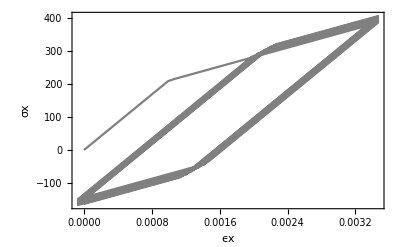

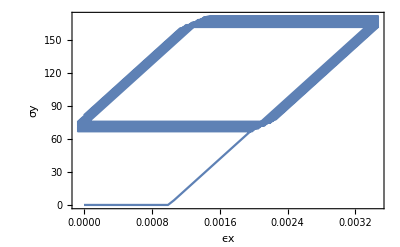

```mathematica
solpsx3d=Table[epsvec3d[[i,1,1]],{i,1,Length[epsvec3d]}];
solsigx3d=Table[sigvec3d[[i,1,1]],{i,1,Length[sigvec3d]}];
d3=ListLinePlot[Table[Tooltip[{solpsx3d[[i]],solsigx3d[[i]]}],{i,1,Length[solpsx3d]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx","σx"},PlotStyle->Gray]
solpsy3d=Table[epsvec3d[[i,1,1]],{i,1,Length[epsvec3d]}];
solsigy3d=Table[sigvec3d[[i,2,2]],{i,1,Length[sigvec3d]}];
ListLinePlot[Table[Tooltip[{solpsy3d[[i]],solsigy3d[[i]]}],{i,1,Length[solpsy3d]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx","σy"}]
```

```mathematica
deps={{0.0000353745,0,0},{0,0,0},{0,0,0}}2;
(*epst={{0.0000353745,0,0},{0,0,0},{0,0,0}}2 15;*)
epst={{0.,0,0},{0,0,0},{0,0,0}};
epsp={{0,0,0},{0,0,0},{0,0,0}}/2;
young=210000;
nu=0.;
sigy=210;
hard=0.;
epsvec={};
sigvec={};
hardvec={};
For[i=1,i<1000,i++,

hard0=hard;
{eps,stress,hard,Dep,Nvec}=ApplyStrainComputeStressPlaneStrain2[epst,epsp,young,nu,hard0];
(*hard+=hard0;*)
diff=Simplify[De-Dep];
epsp=epst-eps;
AppendTo[epsvec,epst];
AppendTo[sigvec,stress];
AppendTo[hardvec,hard];
If[ Mod[i,50]==0,
deps*=-1;
];
epst+=deps;
];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

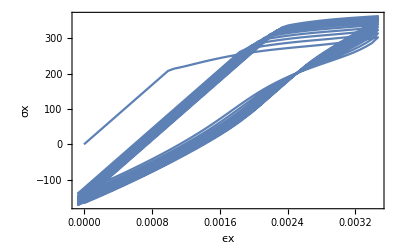

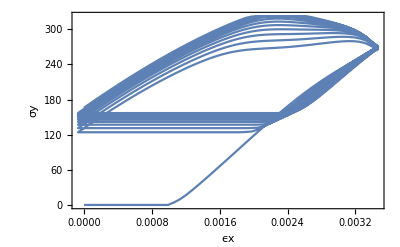

```mathematica
solpsx=Table[epsvec[[i,1,1]],{i,1,Length[epsvec]}];
solsigx=Table[sigvec[[i,1,1]],{i,1,Length[sigvec]}];
pa=ListLinePlot[Table[Tooltip[{solpsx[[i]],solsigx[[i]]}],{i,1,Length[solpsx]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx","σx"}]
solpsy=Table[epsvec[[i,1,1]],{i,1,Length[epsvec]}];
solsigy=Table[sigvec[[i,2,2]],{i,1,Length[sigvec]}];
ListLinePlot[Table[Tooltip[{solpsy[[i]],solsigy[[i]]}],{i,1,Length[solpsy]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx","σy"}]
```

```mathematica
deps={{0.0000353745,0,0},{0,0,0},{0,0,0}}2;
(*epst={{0.0000353745,0,0},{0,0,0},{0,0,0}}2 15;*)
epst={{0.,0,0},{0,0,0},{0,0,0}};
epsp={{0,0,0},{0,0,0},{0,0,0}}/2;
young=210000;
nu=0.;
sigy=210;
hard=0.;
epsvec={};
sigvec={};
hardvec={};
For[i=1,i<1000,i++,

hard0=hard;
{eps,stress,hard,Dep,Nvec}=ApplyStrainComputeStressPlaneStress[epst,epsp,young,nu,hard0];
(*hard+=hard0;*)
diff=Simplify[De-Dep];
epsp=epst-eps;
AppendTo[epsvec,epst];
AppendTo[sigvec,stress];
AppendTo[hardvec,hard];
If[ Mod[i,50]==0,
deps*=-1;
];
epst+=deps;
];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

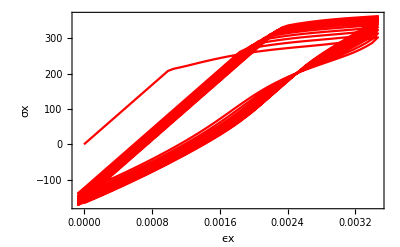

-Graphics-

```mathematica
solpsx=Table[epsvec[[i,1,1]],{i,1,Length[epsvec]}];
solsigx=Table[sigvec[[i,1,1]],{i,1,Length[sigvec]}];
pe=ListLinePlot[Table[Tooltip[{solpsx[[i]],solsigx[[i]]}],{i,1,Length[solpsx]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx","σx"},PlotStyle->Red]
solpsy=Table[epsvec[[i,1,1]],{i,1,Length[epsvec]}];
solsigy=Table[sigvec[[i,2,2]],{i,1,Length[sigvec]}];
ListLinePlot[Table[Tooltip[{solpsy[[i]],solsigy[[i]]}],{i,1,Length[solpsy]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx","σy"}]
```

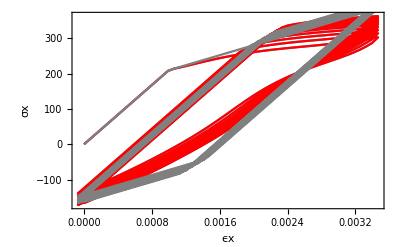

```mathematica
Show[pa,pe,d3]
```